```mathematica
Clear[a];Clear[b];
```

```mathematica
F[x_]:= (x+1)*Log[x+1]-x*Log[x] +(-0.25*x+b*x^2+0.08*x^3)*Exp[-x]
```

```mathematica
M[x_]:=x*Exp[-x]
```

```mathematica
XX[x_]:=(1-Exp[-F'[x]])^(1/(1-M[x]))*(1-M[x])
```

```mathematica
YY[z_]:=If[z < 1/2, Exp[a]*(1-z),1-z*Exp[-a]]
```

```mathematica
ZZ[x_]:=-1/2*(Log[XX[x]]+x(Log[M[x]]+Log[YY[XX[x]]]))
```

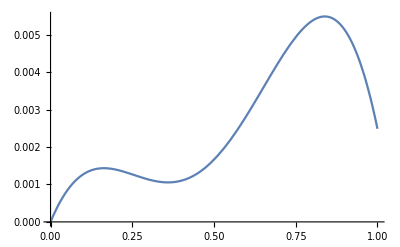

```mathematica
Plot[F[x]-ZZ[x]/.{b->0.08,a->0},{x,0,1}]
```

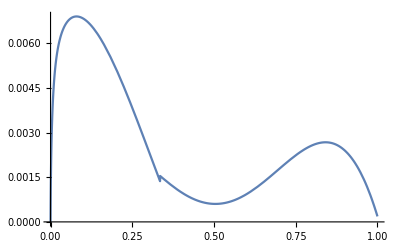

```mathematica
Plot[F[x]-ZZ[x]/.{b->0.045,a->(0.17-0.08)Exp[-1]},{x,0,1}]
```

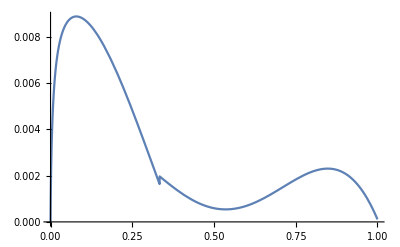

```mathematica
Plot[F[x]-ZZ[x]/.{b->0.033,a->(0.17-0.045)Exp[-1]},{x,0,1}]
```

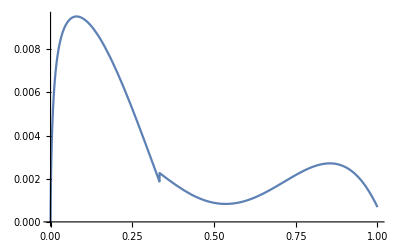

```mathematica
Plot[F[x]-ZZ[x]/.{b->0.03,a->(0.17-0.033)Exp[-1]},{x,0,1}]
```

```mathematica
4*Exp[-0.14Exp[-1]]
```

3.7992

```mathematica
4*Exp[-0.09Exp[-1]]
```

3.86973